```mathematica
Get["FernandoDuarte`LongRunRisk`"]
(*automatically use MaTeX instead of built-in LaTeX in inline/displayed formula cells*)
UsingFrontEnd[
	$useMaTeXMag=1;
	$useMaTeXBaselineShift=0;
	$useMaTeXMag=1.44; (*x^2 and x have the~same size in a Text cell*)
	$useMaTeXBaselineShift=-0.12;  (*aligns x^2 with x in a Text cell*)
	$useMaTeXQ=True;
	Module[{$s},
	Quiet[
	InputAssistant`TeXStringToBoxes//Unprotect;
	InputAssistant`TeXStringToBoxes[$s_String]/;TrueQ@$useMaTeXQ=.;
	InputAssistant`TeXStringToBoxes//Protect;
	InputAssistant`TeXStringToBoxes//Unprotect;
	InputAssistant`TeXStringToBoxes[$s_String]/;TrueQ@$useMaTeXQ:=AdjustmentBox[ToBoxes@MaTeX[$s,Magnification->$useMaTeXMag],BoxBaselineShift->$useMaTeXBaselineShift];
	InputAssistant`TeXStringToBoxes//Protect;
	]];
	(*preamble for MaTeX to use in LaTeX files*)
	preambleTeX={
	"\\usepackage{color}",
	"\\usepackage{microtype}"
	};
]
```

# Interacting with Models

## A general model specification

In this section, we define the most general form of the model that nests all of the specifications we consider. The files that define this general form are in the folder /Kernel/Model, and are:

Parameters.wl | defines the parameters of the model
Shocks.wl | defines the exogenous shocks
ExogenousEq.wl | defines the exogenous variables and their processes
EndogenousEq.wl | defines the endogenous variables

Files that define all the elements of the general model.

### Parameters

The file Parameters.wl creates one public symbols for each parameter of the model in the context "FernandoDuarte`LongRunRisk`Model`Parameters`". The variable $parameters is a list with the SymbolName of each of these parameters.

The private symbol paramAssumptions has restrictions that must be satisfied by the parameters. For example, the discount rate parameter delta must be between 0 and 1, which corresponds to the condition   0<delta &&delta<1 in paramAssumptions.

The exogenous variables are:

$parameters

```mathematica
paramAssumptions = 
	(*preferences*)delta>0 && delta<1 && psi>0 && gamma>0 && theta!=0 &&
	(*process for x*)rhox>-1 && rhox<1 && 
	(*process for pi*) rhop>-1 && rhop<1 && 
	(*process for pibar*)rhopbar>-1 && rhopbar<1 && 
	(*process for sg*)rhog>-1 && rhog<1 &&
	(*process for sx*)vx>-1 && vx<1 && Esx>=0 && phisxs>=0 &&
	(*process for sc*)vc>-1 && vc<1 && Esc>=0 && phiscv>=0 &&
	(*process for sp*)vp>-1 && vp<1 && Esp>=0 && phispw>=0;
```

### Exogenous shocks

We collect all exogenous shocks in a vector  of shocks that are not stock-specific, and a vector  that has shocks to the dividends of stocks:

We identify each shock as the main driver of one of the exogenous processes or, alternatively, as simply a label based on what equation they enter without ascribing any particular interpretation: 
: Long-run risk shock
: Inflation shock
: Expected inflation shock
: Consumption shock
: NRC shock
: Shock to the volatility of long-run risk
: Shock to the volatility of consumption growth
: Shock to the volatility of inflation
: Shock to the dividend of stock

The vector  is i.i.d. standard normal

where we use  to denote the conformable identity matrix. The vector  is also iid standard normal

Each element of  is allowed to be correlated with  with

All elements of  different from  are independent of all elements of .

The file Shocks.wl creates the public symbol eps for the vector of shocks in the context "FernandoDuarte`LongRunRisk`Model`Shocks`". The different shocks are represented by indexing the symbol eps with the corresponding string. For example, eps["x"] is the shock to long-run risk and eps["pi"] is the shock to inflation. Their values at time t is represented by eps["x"][t] and eps["pi"][t].

The distribution of shocks is defined by a set of transformation rules in the public symbol rulesE. The end-user should never have the need to use rulesE.

```mathematica
(* define distribution of exogenous shocks *)
(*for a normal distribution, we only need rules for how to compute expectations of products of shocks*)
rulesE[t_]:={Subscript[ε, c][t]Subscript[ε, d][t,i_]->taugd[i],Subscript[ε, _][t,___]->0,Subscript[ε, _][t,___]^n_Integer->Expectation[x^n,x\[Distributed]NormalDistribution[0,1]]}(*note: also in llr.wl*)
```

### Exogenous processes

The file ExogenousEq.wl creates public symbols that end in "eq" (short for equation) in the context "FernandoDuarte`LongRunRisk`Model`ExogenousEq`". These symbols define the processes for the exogenous variables. The variable $exogenousEq is a list with the SymbolName of each of these variables.

Private symbols with the same names as the public symbols but without the "eq" at the end represent the actual variable rather than the equation that defines it. So for example, long-run risk is x[t] and the equation that defines the process for long-run risk is xeq[t].

The exogenous variables are:

Long-run risk

```mathematica
xeq[t_]:=rhox x[t-1]+rhoxpbar(pibar[t-1]-mupbar)+
phix Sqrt[sx[t-1]+Esx^2]Subscript[ε, x][t] +
phixc Sqrt[sc[t-1]+Esc^2]Subscript[ε,c][t]
```

Inflation

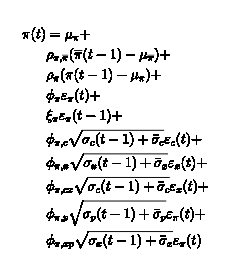

```mathematica
pieq[t_]:=mup+
rhoppbar (pibar[t-1]-mupbar)+
rhop(pi[t-1]-mup)+
phip Subscript[ε, p][t]+
xip Subscript[ε, p][t-1]+
phipc Sqrt[sc[t-1]+Esc^2] Subscript[ε, c][t]+
phipx Sqrt[sx[t-1]+Esx^2]Subscript[ε, x][t] +
phipcx Sqrt[sc[t-1]+Esc^2]Subscript[ε, x][t] +
phipp Sqrt[sp[t-1]+Esp^2]Subscript[ε, p][t]+
phipxp Sqrt[sx[t-1]+Esx^2]Subscript[ε, p][t]
```

Expected inflation

```mathematica
pibareq[t_]:= mupbar+
rhopbar(pibar[t-1]-mupbar)+ 
rhopbarx x[t-1]+
phipbarp Subscript[ε, p][t]+
phipbarc Sqrt[sc[t-1]+Esc^2] Subscript[ε, c][t]+ 
phipbarx Sqrt[sx[t-1]+Esx^2]Subscript[ε, x][t]+
phipbarcx Sqrt[sc[t-1]+Esc^2]Subscript[ε, x][t]+
phipbarpb Sqrt[sp[t-1]+Esp^2]Subscript[ε,b][t]+
phipbarxb Sqrt[sx[t-1]+Esx^2]Subscript[ε,b][t]+
phipbarxp Sqrt[sx[t-1]+Esx^2]Subscript[ε,p][t]
```

Real consumption growth

```mathematica
dceq[t_]:= muc+
rhocx x[t-1]+
rhocp(pi[t-1]-mup)+
phic Subscript[ε, c][t]+
phicp Subscript[ε, p][t]+
phicsp sg[t-1] Subscript[ε, p][t]+
xic sg[t-2] Subscript[ε, p][t-1] + 
phics Sqrt[sx[t-1]+Esx^2]Subscript[ε, x][t]+
phicx Sqrt[sx[t-1]+Esx^2] Subscript[ε, c][t]+
phicc Sqrt[sc[t-1]+Esc^2] Subscript[ε, c][t]+
phicpc Sqrt[sp[t-1]+Esp^2] Subscript[ε, c][t]+
phicpp Sqrt[sp[t-1]+Esp^2] Subscript[ε, p][t]
```

Nominal-real covariance (NRC)

```mathematica
sgeq[t_]:= Esg + 
rhog(sg[t-1]-Esg)+
phig Subscript[ε,g][t]
```

Stochastic volatility of long-run risk

```mathematica
sxeq[t_]:= vx sx[t-1]+
phisxs Subscript[ε, s][t]
```

Stochastic volatility of consumption growth

```mathematica
sceq[t_]:= vc sc[t-1]+
phiscv Subscript[ε, v][t]
```

Stochastic volatility of inflation

```mathematica
speq[t_]:= vp sp[t-1]+
vpp (pi[t-1]-mup)+
vppbar (pibar[t-1]-mupbar)+
phispw Subscript[ε, w][t]
```

Real dividend growth

We index stocks by  with the convention that  corresponds to the aggregate stock market. The process for real dividend growth of stock  is

```mathematica
ddeq[t_,i_]:= mud[i]+
rhodx[i]x[t-1]+
rhodp[i](pi[t-1]-mup)+ 
phidc[i] Subscript[ε, c][t]+ 
phidp[i] Subscript[ε, p][t]+
phidsp[i] sg[t-1]Subscript[ε, p][t]+
xid[i] sg[t-2] Subscript[ε, p][t-1]+
phids[i] Sqrt[sx[t-1]+Esx^2]Subscript[ε, x][t]+
phidxc[i] Sqrt[sx[t-1]+Esx^2]Subscript[ε, c][t]+
phidcc[i] Sqrt[sc[t-1]+Esc^2] Subscript[ε, c][t]+ 
phidpc[i]  Sqrt[sp[t-1]+Esp^2] Subscript[ε, c][t]+
phidpp[i] Sqrt[sp[t-1]+Esp^2] Subscript[ε, p][t]+
phidxd[i] Sqrt[sx[t-1]+Esx^2]Subscript[ε, d][t,i]+ 
phidcd[i] Sqrt[sc[t-1]+Esc^2] Subscript[ε, d][t,i] +
phidpd[i] Sqrt[sp[t-1]+Esp^2] Subscript[ε, d][t,i]
```

Parameter assumptions

```mathematica
modelAssumptions = 
(*process for x*)rhox>=0 && rhox<1 && Esx>=0 && 
(*process for pi*)mup>=0 && rhop>=0 && rhop<1 && rhoppbar>=0 && Esc>=0 && 
(*process for pibar*)mupbar>=0 && rhopbar>=0 && rhopbar<1 && 
(*process for dc*)muc>=0  && rhog>=0 && rhog<1 && 
(*process for sx*)vx>=0 && vx<1 && 
(*process for sc*)vc>=0 && vc<1  && 
(*process for sp*)Esp>=0 && vp>=0 && vp<1  && 
(*preferences*)theta!=0 && psi>1 && delta>0 && delta<1 && gamma>0 && 
(*coefficients of wc*)Element[Subscript[A, s___],Reals]  && 
(*coefficients of pd*)Element[Subscript[D, s___][i___],Reals] && 
(*coefficients of real bond prices*)Element[Subscript[R, s___][n___],Reals] && 
(*coefficients of nominal bond prices*)Element[Subscript[P, s___][n___],Reals] && 
(*shocks*)Element[Subscript[ε, k___][t___],Reals] && 
(*linearization constants*)
Subscript[κ, 0]>0 && Subscript[κ, 0]<1 && 
Subscript[κ, 1]>0&& Subscript[κ, 1]<1 && 
Subscript[κ,0,m][i___]>0 && Subscript[κ,0,m][i___]<1 && 
Subscript[κ,1,m][i___]>0&& Subscript[κ,1,m][i___]<1 ;
```

### Endogenous processes

The file EndogenousEq.wl creates public symbols that end in "eq" (short for equation) in the context "FernandoDuarte`LongRunRisk`Model`EndogenousEq`". These symbols define the processes for the endogenous variables. The variable $exogenousEq is a list with the SymbolName of each of these variables.

Private symbols with the same names as the public symbols but without the "eq" at the end represent the actual variable rather than the equation that defines it. So for example, wc[t] represents the wealth-consumption ratio, and the equation that defines its process is given by wceq[t].

## Pre-defined specifications

Models | is an Association with pre-defined models
Info[Models] | displays some model info in human-readable format
XXXX | XXXX

Pre-defined models.

The general model nests several models in the literature. The file Catalog.wl has a public symbol called models that contains the parameter values, state variables, and additional metadata for some of these models.

The file also has a variable called modelsExtraInfo that has optional information about the models that can be used to speed up computations.

Models is an Association with pre-defined models. In turn, each model is itself given by an Association:

```mathematica
Models["BY"]
```

To display some of the models' information in a more user-friendly format, use Info:

```mathematica
Info[Models]
```

## Creating a new model

newModel[modelName] | processes and saves a new model
XXXX | XXXX

XXXX.

To create a new model, one can simply duplicate an existing model in Catalog.wl and edit it with the new model's information. This can be done by hand by copying and pasting inside the file, or programmatically using Mathematica commands.

In either case, once the new model is created, it is not yet ready to be used. Before it can be used, it has to be "processed" and "saved". Processing a model means pre-computing a number of things that make future calculations faster. Once these pre-computations are done, if we want to have these pre-calculations available the next time we restart the Kernel, they have to be saved in the file Models.wl inside the folder /Resources.

If the new model has been added to Catalog.wl, to process and save a new model, the user must run newModel[modelNameString], where modelNameString is the string given by Keys@models.

If the new model is in an Association called modelName, then newModel[modelNameString] processes and saves the new model.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

FernandoDuarte/LongRunRisk

FernandoDuarte`LongRunRisk`

FernandoDuarte/LongRunRisk/tutorial/InteractingwithModels

### Keywords